## Genetic Algorithms

### Background

Genetic Programming (abbr. GP) essentially refers to “evolving” a program to do a particular task using natural selection and a fitness function. Search space is vast and there is no way to check all possibilities. Most GP approaches make use of programs represented as a tree structure. So WL is a good choice.

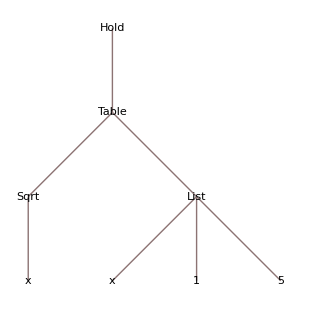

```mathematica
Hold[Table[Sqrt[x], {x, 1, 5}]]//TreeForm
```

To visualise tree structures of programs, we can use the ‘Hold’ function to prevent evaluation. See https://reference.wolfram.com/language/guide/EvaluationControl.html for more information. But before generating programs, let’s start with the most simple genetic program: evolving a string.

### Simple Genetic Program (Nature of Code)

Darwinian Natural Selection has three main properties:

Heredity - children must receive the properties of their parents.

Variation - there must be a variety of traits present in the population or a means to introduce variation

Selection - some members of the population must be able to pass down genetic material to the next generation. (in essence, “survival of the fittest”)

Let’s try to “evolve” a string. Let’s consider our string to be “algorithm”. First we need to create a population of ‘n’ elements with random virtual genetic material.

```mathematica
StringLength["algorithm"]
```

9

We can generate a population of 100 random 9 character strings:

```mathematica
RandomString[length_]:=StringJoin@@RandomChoice[CharacterRange["a", "z"], length]
```

```mathematica
RandomString[9]
```

sacejlybm

```mathematica
population=Table[RandomString[9], 100];
```

We need to select some members from the population for the next generation. We can do this by using a fitness function. In this case, we can define the fitness function as the number of common characters between the guess and the target word. Alternatively, something like edit distance could also be used, which pretty much measures how far apart two words are. Since edit distance is always less than or equal to the length of the target string, we can make use of the following function to measure fitness:

```mathematica
Fitness[guess_, target_]:=StringLength[target]-EditDistance[guess, target]
```

```mathematica
Fitness["algommmmm", "algorithm"]
```

5

Now selection of parents for the next generation and reproduction using them. For each new element of the next generation, we can pick two parents. We can assign each member of the previous generation some probability that it will be picked as a parent of the next element based on its fitness.

```mathematica
Probabilities[fitness_]:=fitness/Total[fitness]
```

```mathematica
ChooseParent[fitness_, population_]:=RandomChoice[Probabilities[(fitness/@population)]->population]
```

```mathematica
Fitness[#,"algorithm"]&/@population
```

{0,0,0,1,0,0,1,0,2,0,1,0,0,1,0,1,1,0,0,1,1,1,1,1,0,0,1,0,1,0,0,1,0,0,1,1,0,1,0,0,0,1,1,0,1,1,1,1,0,1,0,0,0,0,1,0,0,1,0,1,0,0,0,1,0,1,1,0,0,0,0,1,0,2,1,0,0,2,0,1,0,1,0,1,0,0,0,1,0,1,1,0,0,0,1,1,0,0,1,0}

```mathematica
ChooseParent[Fitness[#, "algorithm"]&, population]
```

lxinohgmv

Reproduction (Darwinian) has two parts: crossover and mutation. Crossover just creates an offspring with characteristics inherited from both parents. Mutation introduces some external variation by mutating some characteristics.

We need a function for crossover, which takes two parents and returns an offspring that inherits characteristics from both parents. There’s many ways to do this. We could partition both words and combine halves. Instead we could go character-by-character, picking randomly between each parent for the child’s character at that particular index. For now, we’ll use the latter, but in the future, different reproduction functions could be explored.

```mathematica
Crossover[father_, mother_]:=StringJoin@@Table[RandomChoice[{Characters[father][[index]], Characters[mother][[index]]} ], {index, 1, Min[StringLength[father], StringLength[mother]]}]
```

```mathematica
Crossover["hello", "world"]
```

wollo

For mutation, let’s randomly change characters depending on a ‘mutation rate’ or threshold.

```mathematica
Mutate[child_, rate_]:=StringJoin@@Table[RandomChoice[{1-rate, rate}->{Characters[child][[index]], RandomChoice[CharacterRange["a", "z"]]}],{index, 1, StringLength[child]}]
```

```mathematica
Table[Mutate["wollo", 0.01], 100]
```

{wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wolxo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,vollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wwllo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wolzo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wallo,wollo,wollo,wollo,wollo,wollo,wtllo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wtllo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo,wollo}

With a mutation rate of 1%, a few children have mutations. For example, “wolxo” introduces the character ‘x’ into the population. Mutations are essential to evolution.

Now, let’s try to consolidate the processes of crossover and mutation into a single reproduction function:

```mathematica
Reproduce[father_, mother_, mutation_]:=Mutate[Crossover[father, mother], mutation]
```

```mathematica
Reproduce["hello", "world", 0.1]
```

weslo

The character ‘s’ is introduced as a mutation!

Let’s put everything together:

```mathematica
target="algorithm";
mutationRate=0.05;
populationSize=100;
fitness=Fitness[#, target]&;
```

```mathematica
population=Table[RandomString[StringLength[target]], populationSize];
```

```mathematica
Mean[fitness/@population]//N
```

0.35

```mathematica
nextGeneration=Table[Reproduce[ChooseParent[fitness, population], ChooseParent[fitness, population], mutationRate], populationSize];
```

```mathematica
Mean[fitness/@nextGeneration]//N
```

1.12

In a single generation, the fitness improved from 0.35 to 1.12. Not bad! (Mutation rate = 5%). Now let’s run this process for more generations.

```mathematica
NewGeneration[fitness_, previous_, mutation_]:=Table[Reproduce[ChooseParent[fitness, previous], ChooseParent[fitness, previous], mutation], Length[previous]];
```

```mathematica
evolution=NestList[NewGeneration[fitness, #, mutationRate]&, population, 50];
```

{0.35,1.06,1.29,1.58,1.73,2.16,2.47,2.55,2.64,2.97,3.17,3.35,3.62,3.55,3.43,3.64,3.58,3.65,3.69,3.75,3.99,3.81,3.67,3.86,3.96,3.94,4.06,4.12,4.37,4.24,4.36,4.55,4.51,4.5,4.52,4.53,4.64,4.81,4.88,4.64,4.42,4.35,4.5,4.76,4.84,5.01,5.11,5.17,5.19,5.1,5.}

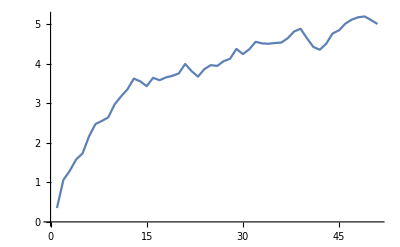

```mathematica
original=N[Mean[fitness/@#]]&/@evolution
ListLinePlot[original]
```

```mathematica
MaximalBy[Last[evolution], fitness]
```

{algocuthm,algoorthm,algourihm,algoorthm,algxorthm,algoxlthm,algojrthm,algoopthm,algoozthm}

The words are certainly closer to ‘algorithm’ and average about 5 characters correct out of the 9. Let’s consider a lower mutation rate:

```mathematica
fewMutations=NestList[NewGeneration[fitness, #, 0.02]&, population, 50];
```

{0.35,1.08,1.46,1.72,2.12,2.48,2.75,3.2,3.24,3.54,3.87,3.91,4.25,4.48,4.74,5.07,5.18,5.37,5.37,5.53,5.84,6.07,6.23,6.17,6.39,6.52,6.45,6.63,6.79,6.89,6.86,6.85,6.77,6.85,6.9,6.98,7.26,7.27,7.03,6.95,6.91,7.08,7.12,7.09,7.05,7.16,7.28,7.2,7.22,7.2,7.23}

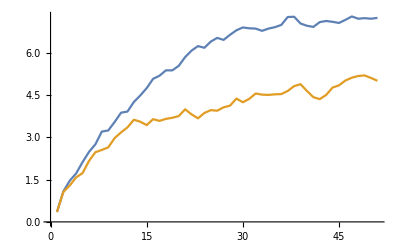

{algorithm,algorithm,algorithm,algorithm,algorithm,algorithm,algorithm,algorithm,algorithm,algorithm}

```mathematica
updated=N[Mean[fitness/@#]]&/@fewMutations
ListLinePlot[{updated, original}]
MaximalBy[Last[fewMutations], fitness]
```

Surprisingly, that does better. Thus, by tweaking parameters, we can arrive at an algorithm able to evolve “algorithm”. The average fitness is about 7.23, but we’ve managed to evolve the target string. While a high mutation rate allows you to get more variability and find target characters that may not be present in the population, it does more harm in fit generations by probably reducing the fitness of an already fit offspring.

By adjusting how genetic material is stored and combined as well as the fitness function, we can create GP solutions for a variety of problems.

NOTE: Genotype is genetic material, Phenotype is physical characteristics (observable).

### Small Improvements

#### Stopping evolution after target has been reached

```mathematica
generations=NestWhileList[NewGeneration[fitness, #, 0.01]&, population, Not[MemberQ[#, target]]&];
Length[generations]-1
N[Mean[fitness/@Last[generations]]]
```

35

6.87

This genetic program can take anywhere between 10-150 trials depending on lucky mutations and crossover.

{13,19,24,22,31,31,29,79,30,80}

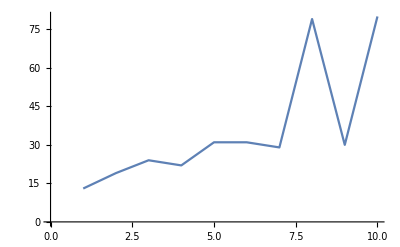

```mathematica
Table[Length[NestWhileList[NewGeneration[fitness, #, rate]&, population, Not[MemberQ[#, target]]&]]-1, {rate, 0.01, 0.10, 0.01}]
ListLinePlot[%]
```

#### Exponential fitness function

```mathematica
newFitness=Exp[fitness[#]]&;
```

```mathematica
generations=NestWhileList[NewGeneration[newFitness, #, 0.01]&, population, Not[MemberQ[#, target]]&];
Length[generations]-1
N[Mean[fitness/@Last[generations]]]
```

21

7.5

Old, linear fitness function (10 trials)

```mathematica
Table[Length[NestWhileList[NewGeneration[fitness, #, 0.02]&, population, Not[MemberQ[#, target]]&, 1, 100]]-1, 10]
```

{16,18,53,100,69,20,48,9,19,35}

New, exponential fitness function (10 trials)

```mathematica
Table[Length[NestWhileList[NewGeneration[newFitness, #, 0.02]&, population, Not[MemberQ[#, target]]&, 1, 100]]-1, 10]
```

{20,17,100,30,100,10,100,11,100,15}

It’s difficult to conclude which one performs better given such a limited population size and number of trials.

One important issue with genetic programs is that they are quite slow, even when run on simple tasks. As the complexity of the task increases, it may become even more challenging to obtain a good answer within a reasonable period of time. Part of the issue may be unoptimized code. WL may also be slower than other programming languages. However, GP is significantly easier in WL.

### Detour: Context Free Grammars

Grammars - Language for a language. Grammars usually make use of symbols or characters, which can be terminal or non-terminal. Grammars also have production rules or replacement rules. For e.g. We could have the non-terminal characters A, B, C and terminal characters a, b, c. We could then have the following production rules:

A → ac

B → aA

C → ABc

Let’s say we have the axiom or starting symbol ‘AC’. Now, we can apply the replacement rules above to get: ‘acABc’. Applying again, we get: ‘acacaAc’. Finally, we get: ‘acacaacc’ by applying production rules recursively. We could also randomly generate sentences based on grammar rules (interesting link: generating a population for a genetic algorithm).

Context-sensitive grammars, on the other hand, have contextual symbols on the right and left hand side which affect production rules.

WL even has its own grammar system for applying rules: https://reference.wolfram.com/language/ref/GrammarRules.html

Formally, a grammar (G) is defined as follows: G = (V, T, P, S), where T is a set of terminal symbols, V is a set of non-terminal symbols (V and T are disjoint sets, i.e. they have no elements in common), P is a set of production rules for replacing members of V with members of V and T. Alphabet is the union of V and T.

```mathematica
start="AC";
```

```mathematica
rules={"A"->"ac", "B"->"aA", "C"->"ABc"};
```

Applying the rule once:

```mathematica
StringReplace[start, rules]
```

acABc

Applying the replacement rules repeatedly until no further rules can be applied:

```mathematica
FixedPointList[StringReplace[#, rules]&, start]
```

{AC,acABc,acacaAc,acacaacc,acacaacc}

By introducing some randomness, we can get variety in the generated strings:

```mathematica
randomRules={"A":>RandomChoice[{"ac", "ab", "a"}], "B"->"aA", "C"->"ABc"};
```

```mathematica
StringReplace[start, randomRules]
```

abABc

```mathematica
FixedPointList[StringReplace[#, randomRules]&, start]
```

{AC,abABc,ababaAc,ababaabc,ababaabc}

Consider a grammar with S as a non-terminal and 0 and 1 as terminals. It has the following production rules:

S → 0S1

S → (empty)

The string 0011 is in the language generated. It’s derivation is: S → 0S1 → 00S11 → 0011. For compactness, we can write  S → 0S1 | (empty). See some more examples here: https://people.cs.clemson.edu/~goddard/texts/theoryOfComputation/6a.pdf

Consider the language with terminal variables T (true) and F (false) and a non-terminal E, with the following production rules:

E → S

E → (E)

E → not E

E → E or E

E → E and E

S  → T

S  → F

Or, simply, E  → S | (E) | not E | E or E | E and E, S  → T | F. Think of E as expression and S as symbol.

This grammar represents simple Boolean expressions. For example, (T or F) and F is in the language generated. Its derivation is: E → E and E → (E) and S  → (E or E) and S → (S or S) and S → (T or F) and F. Although we applied production rules randomly, we should have considered some sort of an order. A leftmost derivation is when a production rule is applied to the leftmost variable. (A rightmost derivation is also defined similarly)

Let’s try to randomly generate some expressions:

```mathematica
logic={"E":>RandomChoice[{"(not E)","(E or E)","(E and E)","S"}], "S":>RandomChoice[{"T", "F"}]};
```

```mathematica
NestList[StringReplace[#, logic]&, "E",5]
```

{E,(E and E),(S and (E or E)),(T and ((not E) or (E and E))),(T and ((not (E or E)) or ((E or E) and S))),(T and ((not ((E and E) or (E and E))) or (((E or E) or (E or E)) and F)))}

```mathematica
unevaluated={"E":>RandomChoice[{"(not E)","(E or E)","(E and E)","S"}]};
```

```mathematica
RandomLogicExpression[depth_]:=StringReplace[Nest[StringReplace[#, unevaluated]&, "E",depth], "E"->"S"]
```

```mathematica
RandomLogicExpression[3]
```

(not ((not S) or (not S)))

```mathematica
(*LogicTree[str_]:=If[str=="S", "S", StringReplace[str, {"(not "~~A__~~")":>Tree["not",{LogicTree[A]}], "(" ~~A__~~" or "~~B__~~")":>Tree["or",{LogicTree[A], LogicTree[B]}], "("~~A__~~" and "~~B__~~")":>Tree["and",{LogicTree[A], LogicTree[B]}]}][[1]]]*)
```

```mathematica
(*LogicTree[list_]:=If[list=={"S"}, "S", Replace[list, 
{{"(","not", A__, ")"}:>Tree["not",{LogicTree[A]}], 
{"(", A__,"or", B__, ")"}:>Tree["or",{LogicTree[A], LogicTree[B]}], 
{"(", A__,"and", B__, ")"}:>Tree["and",{LogicTree[A], LogicTree[B]}]}]]*)
```

Using symbols instead of strings might make handling simpler:

```mathematica
ProductionRules={Symbol["NonTerminal"]:>RandomChoice[{Not[Symbol["NonTerminal"]], And[Symbol["NonTerminal"],Symbol["NonTerminal"]],Or[Symbol["NonTerminal"],Symbol["NonTerminal"]], Symbol["Terminal"]}]};
```

```mathematica
RandomLogicTree[depth_]:=ReplaceAll[Nest[ReplaceAll[#, ProductionRules]&,Symbol["NonTerminal"], depth ], Symbol["NonTerminal"]->Symbol["Terminal"]]
```

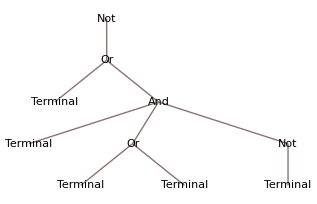

```mathematica
TreeForm[RandomLogicTree[5]]
```

### Evolving Tree Representations of Programs

(Reference: A Field Guide to Genetic Programming)
Arity - number of inputs taken by a function. AND has arity 2 and NOT has arity 1.
Generating populations: full and growth methods, ramped half-and-half method.
Selection: Fitness-proportionate selection (same as the method we had previously implemented) or Tournament selection

Clarification: Genetic Algorithms refer to all programs that incorporate evolution into solving or optimizing a certain task or process. Genetic Programming specifically refers to the applications of Genetic Algorithms in evolving other programs. GP differs a lot from GA in the manner in which mutation and recombination (crossover) are implemented.

Subtree crossover – Given two parents, a random crossover point or node is selected in each parent tree. A child is created identical to the first parent except for the fact that the subtree rooted at the crossover point has been replaced with a copy from the subtree rooted at the crossover point for the second parent. It is possible to return two offspring using this method, however, this is not commonly considered. (other methods discussed in Sections 5.1, 5.3)

Subtree mutation - randomly select a mutation point in the tree and replace it with a randomly generated subtree OR crossover with a random tree (headless chicken crossover). An alternate method of mutation is point mutation, where each node (function) is replaced with another node of equal arity. This is done for all nodes, with a certain probability of point mutation. Point mutation won’t be too useful in our example, however, given the limited number of functions considered (and, not, or).

Terminal set includes constants, variables AND functions with arity 0 (functions that don’t take any arguments) [for e.g. random()]. Another important feature of genetic programs is the manner in which they deal with random values: a terminal known as the ephemeral random constant is introduced, which changes when a new tree is created but remains constant for the rest of the run (more information later).

```mathematica
Terminals={Symbol["A"], Symbol["B"]};
```

```mathematica
NonTerminals={Symbol["ArityAnd"][Symbol["NonTerminal"], Symbol["NonTerminal"]], Symbol["ArityOr"][Symbol["NonTerminal"], Symbol["NonTerminal"]], Symbol["ArityNot"][Symbol["NonTerminal"]]};
```

```mathematica
Individual[depth_, terminals_, nonterminals_]:=ReplaceAll[ReplaceAll[Nest[ReplaceAll[#, Symbol["NonTerminal"]:>RandomChoice[Append[nonterminals, Symbol["Terminal"]]]]&,Symbol["NonTerminal"], depth ], Symbol["NonTerminal"]->Symbol["Terminal"]], Symbol["Terminal"]:>RandomChoice[terminals]]
```

```mathematica
test=Individual[3, Terminals, NonTerminals]
```

ArityAnd[ArityOr[ArityNot[A],ArityNot[B]],ArityOr[A,ArityOr[B,A]]]

```mathematica
ExpressionTree[test]
```

-Graphics-

```mathematica
Response[individual_, terminals_, nonterminals_]:=ReplaceAll[ReplaceAll[individual, nonterminals], terminals]
```

```mathematica
Response[test, {Symbol["A"]->False,Symbol["B"]->True}, {Symbol["ArityAnd"]->And, Symbol["ArityOr"]->Or, Symbol["ArityNot"]->Not}]
```

True

```mathematica
Gene[individual_]:=SubPart[individual, 3]
SubPart[individual_]:=If[depth==0, individual, SubPart[individual[[RandomInteger[{1,Length[individual]}]]], depth-1]]
```

```mathematica
Gene[test]
```

Part::partd: Part specification A⟦1⟧ is longer than depth of object.

A⟦1⟧

```mathematica
RandomInteger[1]
```

1